```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Sat 3 Feb 2018 15:34:08

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 13

[1] C. Arangala, Exploring Linear Algebra: Labs and Projects with Mathematica ®, 1st ed. Boca Raton: Chapman and Hall/CRC, 2014.

-Graphics-

## 3 Vector Spaces

## Lab 11: Vector Spaces and Subspaces

### Introduction

Let V be a nonempty set which addition and scalar multiplication are defined. If the following properties hold for ∀u⃗, v⃗, w⃗∈V and all scalars k, l∈F then V is a vector space.
1. u⃗+(v⃗+w⃗)=(u⃗+v⃗)+w⃗
2. u⃗+v⃗=v⃗+u⃗
3. ∃OverVector[0]∈V s.t. v⃗+OverVector[0]=v⃗ for ∀v⃗∈V.
4. For ∀∈V, ∃ -v⃗∈V s.t. v⃗+(-v⃗)=OverVector[0].
5. a(b v⃗)=(a b)v⃗
6. 1 v⃗=v⃗, where 1 denotes the multiplicative identity in F.
7. a(u⃗ + v⃗) = a u⃗ + k v⃗
8. (a+b)v⃗=a v⃗+a v⃗

Exercises: Let V=R^2 and u=(u_1,u_2), v=(v_1,v_2) in V. Define addition as u+v=(u_1+v_1,v_2) and scalar multiplication as k u=(k u_1,k u_2).

a.

```mathematica
SCARA[u+v,{u+v->{Subscript[u, 1]+Subscript[v, 1],Subscript[v, 2]}}]
SCMAF[%,RA,{At[2],{u=={1,1},v=={1,2}}},
RA,{At[2],{Subscript[u_, i_]:>u[[i]]}}]
```

u+v=={u_1+v_1,v_2}

u+v=={{1,1}_1+{1,2}_1,{1,2}_2}

u+v=={2,2}

b.

```mathematica
v=={0,0};
```

Exercises: Let V=M_(2,2), where M_(2,2) is all 2×2 matrices. If u=(u_1 | u_2
u_3 | u_4) and v=(v_1 | v_2
v_3 | v_4). Define addition as u+v=(u_1+v_1 | u_2+v_2
u_3+v_3 | u_4+v_4) and scalar multiplication as k u=(k u_1 | 0
0 | k u_3).

c, d, e, f, g.

Axiom 1

```mathematica
SCARA[u+(v+w),{u==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}}),w==({{Subscript[w, 1], Subscript[w, 2]}, {Subscript[w, 3], Subscript[w, 4]}})},MatrixForm->True]
```

u+v+w==(u_1+v_1+w_1 | u_2+v_2+w_2
u_3+v_3+w_3 | u_4+v_4+w_4)

```mathematica
SCARA[(u+v)+w,{u==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}}),w==({{Subscript[w, 1], Subscript[w, 2]}, {Subscript[w, 3], Subscript[w, 4]}})},MatrixForm->True]
```

u+v+w==(u_1+v_1+w_1 | u_2+v_2+w_2
u_3+v_3+w_3 | u_4+v_4+w_4)

Axiom 2

```mathematica
SCARA[u+v,{u==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},MatrixForm->True]
```

u+v==(u_1+v_1 | u_2+v_2
u_3+v_3 | u_4+v_4)

```mathematica
SCARA[v+u,{u==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},MatrixForm->True]
```

u+v==(u_1+v_1 | u_2+v_2
u_3+v_3 | u_4+v_4)

Axiom 3

```mathematica
SCARA[v+0,{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},MatrixForm->True]
```

v==(v_1 | v_2
v_3 | v_4)

Axiom 4

```mathematica
SCARA[v+w,{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}}),w==({{-Subscript[v, 1], -Subscript[v, 2]}, {-Subscript[v, 3], -Subscript[v, 4]}})},MatrixForm->True]
```

v+w==(0 | 0
0 | 0)

Axiom 5

```mathematica
SCARA[a (b v),{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},MatrixForm->True]
```

a b v==(a b v_1 | a b v_2
a b v_3 | a b v_4)

```mathematica
SCARA[(a b) v,{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},MatrixForm->True]
```

a b v==(a b v_1 | a b v_2
a b v_3 | a b v_4)

Axiom 7

```mathematica
SCARA[1 v,{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},MatrixForm->True]
```

v==(v_1 | v_2
v_3 | v_4)

Axiom 7

```mathematica
SCARA[a(u+v),{u==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},Apply->ExpandAll,MatrixForm->True]
```

a (u+v)==(a u_1+a v_1 | a u_2+a v_2
a u_3+a v_3 | a u_4+a v_4)

```mathematica
SCARA[a u+a v,{u==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},Apply->ExpandAll,MatrixForm->True]
```

a u+a v==(a u_1+a v_1 | a u_2+a v_2
a u_3+a v_3 | a u_4+a v_4)

Axiom 8

```mathematica
SCARA[(a+b)v,{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},Apply->ExpandAll,MatrixForm->True]
```

```mathematica
SCARA[a v+b v,{v==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})},Apply->ExpandAll,MatrixForm->True]
```

a v+b v==(a v_1+b v_1 | a v_2+b v_2
a v_3+b v_3 | a v_4+b v_4)

h.

i.

### Subspaces

If W is a nonempty subset of a vector space V, then W is a subspace of V if under the operatoins of V
1. W is closed under addition and
2. W is closed under scalar multiplication.

Exercises:

a.

b.

```mathematica
({{1, 2}, {2, 4}}).x==({{0}, {0}})
SCMAF[%,RA,{At[1],x==({{Subscript[x, 1]}, {Subscript[x, 2]}})},
Solve,{All,{Subscript[x, 1],Subscript[x, 2]}},IgnoreError->True]
```

{{1,2},{2,4}}.x=={{0},{0}}

{{x_1+2 x_2},{2 x_1+4 x_2}}=={{0},{0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x_2→-x_1/2}}

```mathematica
x==({{Subscript[x, 1]}, {-Subscript[x, 1]/2}})
```

x=={{x_1},{-x_1/2}}

```mathematica
SCARA[x+w,x_->{{Subscript[x, 1]},{-Subscript[x, 1]/2}},Level->{1},Apply->Simplify,MatrixForm->True]
```

w+x==(w_1+x_1
1/2 (-w_1-x_1))

```mathematica
SCARA[a x,x->{{Subscript[x, 1]},{-Subscript[x, 1]/2}},MatrixForm->True]
```

a x==(a x_1
-(a x_1)/2)

c.

### Theorem and Problems

Problem 39. If V is the set of 2×2 invertible matrices then V is a vector space under matrix addition and scalar multiplication of matrices.

Problem 40. The set of 2×2 symmetric matrices under matrix addition and scalar multiplicaiton of matrices is a vector space.

Problem 41. If V is a vector space with u_1 and u_2 vectors in V then a_1 u_1+a_2 u_2+b_1 u_1+b_2 u_2=(a_1+b_1)u_1+(a_2+b_2)u_2 fo any scalar a_1, a_2, b_1, and b_2 are scalars.

Probme 42. If A is a n×n matrix, then the solution set to A x=0 is a subspace fo R^n.

Probme 43. If A is a n×n matrix, then the set of linear combinations of the rows of A is a subspace of R^n.

Theorem 44. If S={v_1,v_2, ..., v_n} is a set of vectors in vector space V, then the set of all linear combinations of vectors in S is a subspace of V.

## Lab 12: Basing It All on Just a Few Vectors

### Introduction

A set S spans a vector space V if ∀v∈V can be represented as a linear combination of s∈S.

A set S is a basis for a vector space V, if
1. S spans V.
2. S is linearly independent.

The dimension of a vector space V, dim[V], is the number of vectors in a basis.

If the number of basis vectors for a vector space is finite we call the vector space finite dimensional, otherwise, infinite dimensional.

### Nullspace

Exercises:

a.

```mathematica
SCARA[NullSpace[A],A==({{1, 2}, {2, 4}}),Apply->Transpose,MatrixForm->True]
```

NullSpace[A]==(-2
1)

The nullity of A is 1.

```mathematica
SCARA[length@NullSpace[A],A==({{1, 2}, {2, 4}})]
SCMAF[%,RA,{At[2],length->Length}]
```

length[NullSpace[A]]==length[{{-2,1}}]

length[NullSpace[A]]==1

b.

```mathematica
SCARA[NullSpace[B],B==({{1, 2, 3}, {4, 5, 6}, {0, 1, 2}}),Apply->Transpose,MatrixForm->True]
```

NullSpace[B]==(1
-2
1)

The nullity of B is 2.

```mathematica
SCARA[length@NullSpace[B],B==({{1, 2, 3}, {4, 5, 6}, {0, 1, 2}})]
SCMAF[%,RA,{At[2],length->Length}]
```

length[NullSpace[B]]==length[{{1,-2,1}}]

length[NullSpace[B]]==1

c.

```mathematica
SCARA[Inverse[A],A==({{1, 2}, {2, 4}})]
```

Inverse::sing: Matrix {{1,2},{2,4}} is singular.

SCMAF::stopped: Stopped due to error.

A^-1=={{1,2},{2,4}}^-1

```mathematica
SCARA[Inverse[B],B==({{1, 2, 3}, {4, 5, 6}, {0, 1, 2}})]
```

Inverse::sing: Matrix {{1,2,3},{4,5,6},{0,1,2}} is singular.

SCMAF::stopped: Stopped due to error.

B^-1=={{1,2,3},{4,5,6},{0,1,2}}^-1

A matrix is invertible iff nullity is 0.

d.

```mathematica
SCARA[length@NullSpace@Transpose@A,A==({{1, 2}, {2, 4}})]
SCMAF[%,RA,{At[2],length->Length}]
```

length[NullSpace[A^T]]==length[{{-2,1}}]

length[NullSpace[A^T]]==1

```mathematica
SCARA[length@NullSpace@Transpose@B,B==({{1, 2, 3}, {4, 5, 6}, {0, 1, 2}})]
SCMAF[%,RA,{At[2],length->Length}]
```

length[NullSpace[B^T]]==length[{{-4,1,3}}]

length[NullSpace[B^T]]==1

The nullity of a matrix is invariant under the transpose operation.

e.

```mathematica
SCARA[NullSpace[M],M==({{1, 0, 5, 0}, {0, 1, 3, -1}, {-2, 0, 1, 4}}),Apply->Transpose,MatrixForm->True]
```

NullSpace[M]==(20
23
-4
11)

```mathematica
SCARA[length@NullSpace@M,M==({{1, 0, 5, 0}, {0, 1, 3, -1}, {-2, 0, 1, 4}})]
SCMAF[%,RA,{At[2],length->Length}]
```

length[NullSpace[M]]==length[{{20,23,-4,11}}]

length[NullSpace[M]]==1

### Rowspace and Columnspace

Exercises:

a.

```mathematica
SCARA[RowReduce[A],A==({{1, 2}, {2, 4}})]
```

RowReduce[A]=={{1,2},{0,0}}

The basis for row space of A is (1
2).

```mathematica
Length@Cases[{{1,2},{0,0}},{0...,1,___}]
```

1

```mathematica
SCARA[MatrixRank[A],A==({{1, 2}, {2, 4}})]
```

MatrixRank[A]==1

b.

```mathematica
SCARA[MatrixRank[A]+length@NullSpace@A,{A==({{1, 2}, {2, 4}})}]
SCMAF[%,RA,{At[2],length->Length}]
```

length[NullSpace[A]]+MatrixRank[A]==1+length[{{-2,1}}]

length[NullSpace[A]]+MatrixRank[A]==2

c.

d.

If an n×n matrix is invertible, then nullity of A is zero and the basis of row space spans R^n.

If an n×n matrix is invertible, then nullity of A is zero and the basis of column space spans R^n.

e.

```mathematica
SCARA[RowReduce[M],M==({{1, 0, 5, 0}, {0, 1, 3, -1}, {-2, 0, 1, 4}})]
```

RowReduce[M]=={{1,0,0,-20/11},{0,1,0,-23/11},{0,0,1,4/11}}

The basis for column space of M is

```mathematica
{({{1}, {0}, {-2}}),({{0}, {1}, {0}}),({{5}, {3}, {1}})};
```

```mathematica
columnSpace[m_]:=Module[{rrm,tm},
rrm=RowReduce[m];
tm=Transpose[m];
Fold[Join[#1,Part[tm,FirstPosition[#2,1]]]&,{},rrm]
]
columnSpace[({{1, 0, 5, 0}, {0, 1, 3, -1}, {-2, 0, 1, 4}})]
```

{{1,0,-2},{0,1,0},{5,3,1}}

f.

```mathematica
SCARA[MatrixRank[M]+length@NullSpace[M],M==({{1, 0, 5, 0}, {0, 1, 3, -1}, {-2, 0, 1, 4}}),RA->{length->Length}]
```

length[NullSpace[M]]+MatrixRank[M]==4

g.

The rank and the nullity of a matrix add up to the number of columns of the matrix.

### Theorems and Problems

Theorem 45. A is invertible iff the nullspace of A=OverVector[0] and nullity(A)=0.

Theorem 46. an n×n matrix A is invertible iff the rowspace of A=R^n and rank(A)=n.

Problem 47. If A is a m×n matrix then rank(A)+nullity(A)=m.

Problem 48. rank(A)=rank(A^T).

If A is an n×n matrix the following are equivalent statements:
1. A is invertible.
2. Det[A]≠0.
3. The rref(A) is Ι_n.
4. A can be writen as a product of elementary matrices.
5. The system A x=b has exactly one solution for all n×1 vectors b.
6. The system A x=0 has only the trivial solution.
7. nullity(A)=0
8. r(A)=R^n, c(A)=R^n, rank(A)=n.

## Lab 13: Linear Transformations

### Introduction

A transformation T:V→W is a mapping between vector spaces V and W.

The transformation is a linear transformation iff
T(OverVector[0])=OverVector[0], ∀v_1,v_2∈V satisfy T(v_1+v_2)=T(v_1)+T(v_2), ∀v∈V and scalar k satisfy T(k v)=k T(v).

We will work with T s.t T=A x. The matrix A is called the standard marix.

### Basic Linear Transformations and Standard Matrices

Exercises:

a.

Demonstration: Change the Dog: Matrix Transformations

Reflection over the x-axis.

```mathematica
Subscript[A, y==0]==({{1, 0}, {0, -1}});
```

Reflection over the y-axis.

```mathematica
Subscript[A, x==0]==({{-1, 0}, {0, 1}});
```

Reflection over the origin.

```mathematica
Subscript[A, 0]==({{-1, 0}, {0, -1}});
```

b.

Dilation

```mathematica
Subscript[A, d]==({{a, 0}, {0, a}})/;a>1;
```

Contraction

```mathematica
Subscript[A, c]==({{a, 0}, {0, a}})/;0<a<1;
```

c.

Reflection over the y=x.

```mathematica
Subscript[A, y==x]==({{0, 1}, {1, 0}});
```

d.

Projection onto the x-axis.

```mathematica
Subscript[A, p,x]==({{1, 0}, {0, 0}});
```

Projection onto the y-axis.

```mathematica
Subscript[A, p,y]==({{0, 0}, {0, 1}});
```

e.

Demonstration: 2D Rotation Using Matrices

```mathematica
Subscript[A, r]==({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
```

f.

Demonstration: Linear Transformations and Basic Computer Graphics

```mathematica
SCARA[Subscript[A, d].Subscript[A, r].Subscript[A, y==x],{Subscript[A, y==x]==({{0, 1}, {1, 0}}),Subscript[A, r]==({{Cos[45°], -Sin[45°]}, {Sin[45°], Cos[45°]}}),Subscript[A, d]==({{3/2, 0}, {0, 3/2}})},MatrixForm->True]
```

A_D.A_R.A_(y==x)==(-3/(2 √2) | 3/(2 √2)
3/(2 √2) | 3/(2 √2))

### One to One Transformations

T is one to one if T(v_1)=T(v_2) implies v_1=v_2.

Exercises:

A transformation is one-to-one, iff the determinant of the standard matrix is not 0.

```mathematica
SCARA[{Det[Subscript[A, y==0]],Det[Subscript[A, x==0]],Det[Subscript[A, 0]],Det[Subscript[A, d]],Det[Subscript[A, c]],Det[Subscript[A, y==x]],Det[Subscript[A, p,x]],Det[Subscript[A, p,y]],Det[Subscript[A, r]]},{Subscript[A, y==0]==({{1, 0}, {0, -1}}),Subscript[A, x==0]==({{-1, 0}, {0, 1}}),Subscript[A, 0]==({{-1, 0}, {0, -1}}),Subscript[A, d]==({{a, 0}, {0, a}}),Subscript[A, c]==({{a, 0}, {0, a}}),Subscript[A, y==x]==({{0, 1}, {1, 0}}),Subscript[A, p,x]==({{1, 0}, {0, 0}}),Subscript[A, p,y]==({{0, 0}, {0, 1}}),Subscript[A, r]==({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})},Apply->Simplify]//Thread
```

{Det[A_(y==0)]==-1,Det[A_(x==0)]==-1,Det[A_0]==1,Det[A_d]==a^2,Det[A_c]==a^2,Det[A_(y==x)]==-1,Det[A_(p,x)]==0,Det[A_(p,y)]==0,Det[A_r]==1}

### Transformations from R^n→R^m

The kernel of transformation T is the set of vector x s.t. T(x)=OverVector[0].

If T:V→W then the range of T is {y|y∈W, and T(x)=y for x∈V}.

Exercises:

a.

```mathematica
T==({{1, -1}, {2, 1}});
```

```mathematica
SCARA[RowReduce[T],T==({{1, -1}, {2, 1}})]
```

RowReduce[T]=={{1,0},{0,1}}

```mathematica
SCARA[NullSpace[T],T==({{1, -1}, {2, 1}})]
```

NullSpace[T]=={}

```mathematica
SCARA[length@NullSpace[T],T==({{1, -1}, {2, 1}}),RA->{length->Length}]
```

length[NullSpace[T]]==0

b.

```mathematica
Subscript[T, A]==({{1, 1, 0}, {0, 2, 0}, {1, 0, -1}});
```

```mathematica
Subscript[T, A].x==Subscript[T, A].y
SCMAF[%,RA,{All,{Subscript[T, A]==({{1, 1, 0}, {0, 2, 0}, {1, 0, -1}}),x==({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}}),y==({{Subscript[y, 1]}, {Subscript[y, 2]}, {Subscript[y, 3]}})}},
SCSolve,{All,{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}}]
```

T_A.x==T_A.y

{{x_1+x_2},{2 x_2},{x_1-x_3}}=={{y_1+y_2},{2 y_2},{y_1-y_3}}

{y_1==x_1,y_2==x_2,y_3==x_3}

Therefore, T_A is one-to-one transformation.

c.

```mathematica
SCARA[NullSpace[Subscript[T, A]],Subscript[T, A]==({{1, 1, 0}, {0, 2, 0}, {1, 0, -1}})]
```

NullSpace[T_A]=={}

```mathematica
SCARA[RowReduce[Subscript[T, A]],Subscript[T, A]==({{1, 1, 0}, {0, 2, 0}, {1, 0, -1}})]
```

RowReduce[T_A]=={{1,0,0},{0,1,0},{0,0,1}}

### Theorems and Problems

In all of the following statements, T_A:R^n→R^n is defined by multiplication by the n×n standard matrix A.

Theorem 49. T_A is one to one iff A is invertible.

Theorem 50. If A is an invertible matrix then the kernel of T_A=R^n.

Theorem 51. If A is an invertible matrix then nullity(T_A)=0.

Theorem 52. If T_1:R^n→R^m and T_2:R^m→R^p are two linear transformations then T_2∘T_1 is a linear transformation.

Theorem 53. T_1(x_1,x_2)=(x_1+k_1,x_2+k_2) is a linear transformation where k_1 and k_2 are nonzero scalars.

## Lab 14: Eigenvalues and Eigenspaces

### Introduction

Given a square matrix A, we can calculate the eigenvalues of A by finding the values for λ s.t. A.x=λ x. The λ’s are the eigenvalues for A and each eigenvalue has a corresponding eigenvector x.

Exercises:

a.

```mathematica
SCARA[Det[A-λ Ι],{A==({{1, 2, 3}, {0, 5, 6}, {0, 0, 0}}),Ι==IdentityMatrix[3]}]
SCMAF[%,RA,{At[1],Det[A-Ι λ]==0},
SCSolve,{All,λ}]
```

Det[A-Ι λ]==-λ (5-6 λ+λ^2)

0==-λ (5-6 λ+λ^2)

{{λ==0},{λ==1},{λ==5}}

```mathematica
SCARA[Eigenvalues[A],A==({{1, 2, 3}, {0, 5, 6}, {0, 0, 0}})]
```

Eigenvalues[A]=={5,1,0}

```mathematica
SCARA[Eigenvalues[B],B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})]
```

Eigenvalues[B]=={5,5,1}

```mathematica
SCARA[Eigenvalues[M],M==({{1, 2}, {2, 4}})]
```

Eigenvalues[M]=={5,0}

b.

A matrix is singular iff its eigenvalue is 0.

Prof. 
A singular ⇔ det(A)=0 ⇔ det(A-0 I) ⇔ eigenvalue is 0.

c.

For matrix B,

```mathematica
SCARA[Eigensystem[B],B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})]
```

Eigensystem[B]=={{5,5,1},{{1,2,0},{0,0,0},{1,0,0}}}

```mathematica
SCARA[B-λ Ι,{B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}}),λ==5,Ι==IdentityMatrix[3]},MatrixForm->True]
SCMAF[%,NullSpace,All,Level->{1},Apply->Transpose]
```

B-Ι λ==(-4 | 2 | 3
0 | 0 | 6
0 | 0 | 0)

NullSpace[B-Ι λ]^T==(1
2
0)

```mathematica
SCARA[B-λ Ι,{B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}}),λ==1,Ι==IdentityMatrix[3]},MatrixForm->True]
SCMAF[%,NullSpace,All,Level->{1},Apply->Transpose]
```

B-Ι λ==(0 | 2 | 3
0 | 4 | 6
0 | 0 | 4)

NullSpace[B-Ι λ]^T==(1
0
0)

For matrix M,

```mathematica
SCARA[Eigensystem[M],M==({{1, 2}, {2, 4}})]
```

Eigensystem[M]=={{5,0},{{1,2},{-2,1}}}

```mathematica
SCARA[M-λ Ι,{M==({{1, 2}, {2, 4}}),λ==5,Ι==IdentityMatrix[2]},MatrixForm->True]
SCMAF[%,NullSpace,All,Level->{1},Apply->Transpose]
```

M-Ι λ==(-4 | 2
2 | -1)

NullSpace[M-Ι λ]^T==(1
2)

```mathematica
SCARA[M-λ Ι,{M==({{1, 2}, {2, 4}}),λ==0,Ι==IdentityMatrix[2]},MatrixForm->True]
SCMAF[%,NullSpace,All,Level->{1},Apply->Transpose]
```

M-Ι λ==(1 | 2
2 | 4)

NullSpace[M-Ι λ]^T==(-2
1)

d.

```mathematica
Dot@@Eigenvectors@({{1, 2}, {2, 4}})
```

0

e.

The trace of matrix and sum of eigenvalues are the same.

```mathematica
Total@Eigenvalues@({{1, 2}, {2, 4}})
```

5

```mathematica
Tr@({{1, 2}, {2, 4}})
```

5

f.

```mathematica
Times@@Eigenvalues@({{1, 2}, {2, 4}})
```

0

```mathematica
Det@({{1, 2}, {2, 4}})
```

0

g.

h.

```mathematica
SCARA[CharacteristicPolynomial[B,x],B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})]
```

CharacteristicPolynomial[B,x]==25-35 x+11 x^2-x^3

i.

```mathematica
SCARA[CharacteristicPolynomial[B,x],B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})]
SCMAF[%,RA,{At[1],CharacteristicPolynomial[B,x]==0},
SCSolve,{All,x}]
```

CharacteristicPolynomial[B,x]==25-35 x+11 x^2-x^3

0==25-35 x+11 x^2-x^3

{{x==1},{x==5},{x==5}}

j.

From definition,

```mathematica
SCARA[det[B-λ Ι],{B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}}),Ι==IdentityMatrix[3]}]
SCMAF[%,RA,{At[2],det->Det},Apply->ExpandAll,
RA,{All,λ->0}]
```

det[B-Ι λ]==det[{{1-λ,2,3},{0,5-λ,6},{0,0,5-λ}}]

det[B-Ι λ]==25-35 λ+11 λ^2-λ^3

det[B]==25

### Cayley-Hamilton Theorem

The Cayley-Hamilton theorem states that substituting the matrix A for λ in this polynomial results in the zero matrix,
p(A)=O.

Exercise:

Show whether B satisfies the Cayley-Hamilton theorem.

```mathematica
SCARA[CharacteristicPolynomial[B,x],B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})]
SCMAF[%,RR,{All,{x->B,B^n_->MatrixPower[B,n]}},
RA,{At[2],B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})},MatrixForm->True]
```

CharacteristicPolynomial[B,x]==25-35 x+11 x^2-x^3

CharacteristicPolynomial[B,B]==25-35 B+11 MatrixPower[B,2]-MatrixPower[B,3]

CharacteristicPolynomial[B,B]==(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Derivation of the inverse calculation equation.

```mathematica
CharacteristicPolynomial[A,x]==∑_(i=0)^n Subscript[c, i] x^i
SCMAF[%,RA,{At[1],CharacteristicPolynomial[A,x]==0},
SCSumChangeLimits,{At[2],{i,1,n-1}},
SCDivEq,{All,x},Apply->SCInSum,
RA,{At[2],{Subscript[c, 0]==(-1)^n Det[A],Subscript[c, n]==1,Power[x,-1]==Inverse[A]}},
SCSolve,{All,A^-1},
SCFactor,{x^n+x ∑_(i=1)^(-1+n) x^(-1+i) Subscript[c, i],x}]
```

CharacteristicPolynomial[A,x]==∑_(i=0)^n x^i c_i

A^-1==(-1)^(1-n)/(x Det[A]) (x^n+x ∑_(i=1)^(-1+n) x^(-1+i) c_i)

A^-1==(-1)^(1-n)/Det[A] (x^(-1+n)+∑_(i=1)^(-1+n) x^(-1+i) c_i)

```mathematica
Thread@Rule[Table[Subscript[c, i],{i,0,3}],CoefficientList[(-1)^3 CharacteristicPolynomial[({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}}),x],x]]
```

{c_0→-25,c_1→35,c_2→-11,c_3→1}

```mathematica
CharacteristicPolynomial[({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}}),x]
```

25-35 x+11 x^2-x^3

```mathematica
B^-1==(-1)^(1-n)/Det[B] ∑_(i=1)^n B^(-1+i) Subscript[c, i]
SCMAF[%,RA,{At[2],{n==3}},Apply->SCEvalSum,
RA,{At[2],Power[B_,n_]/;n>0->MatrixPower[B,n]},
RA,{At[2],{B==({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}})}},
RA,{At[2],Thread@Rule[Table[Subscript[c, i],{i,0,3}],CoefficientList[(-1)^3 CharacteristicPolynomial[({{1, 2, 3}, {0, 5, 6}, {0, 0, 5}}),x],x]]},MatrixForm->True]
```

B^-1==(-1)^(1-n)/Det[B] ∑_(i=1)^n B^(-1+i) c_i

B^-1=={{1/25 (c_1+c_2+c_3),1/25 (2 c_2+12 c_3),1/25 (3 c_2+30 c_3)},{0,1/25 (c_1+5 c_2+25 c_3),1/25 (6 c_2+60 c_3)},{0,0,1/25 (c_1+5 c_2+25 c_3)}}

B^-1==(1 | -2/5 | -3/25
0 | 1/5 | -6/25
0 | 0 | 1/5)

### Theorems and Problems

Theorem 54. A is invertible iff all its eigenvalues are nonzero.

Theorem 55. If λ is an eigenvalue for A then 1/λ_k is an eigenvalue for A^-1.

Problem 56. If λ is an eigenvalue for A then λ^k is an eigenvalue for A^k.

Problem 57. If λ if an eigenvalue for A then λ is an eigenvalue for A^T.

Problem 58. The eigenvalues of a triangular matrix (upper or lower) are the vector space.

Problem 59. If A is an n×n matrix with n distinct eigenvalues then all of the corresponding eigenvectors are linearly independent.

## Lab 15: Markov Chains: An Application of Eigenvalues

### Introduction

A Markov chain is “a stochastic model describing a sequence of possible events in which the probability of each event depends only on the state attained in the previous event.” - Wikipedia.

```mathematica
M==({{0.05, 0.7, 0.46}, {0.75, 0.2, 0.12}, {0.2, 0.1, 0.42}});
```

Exercises:

a, b.

```mathematica
Manipulate[Block[{M=({{.05, .7, .46}, {.75, .2, .12}, {.2, .1, .42}}),x0=({{100}, {0}, {0}})},BarChart[MatrixPower[M,k].x0]],{k,0,20,1}]
```

c.

```mathematica
FixedPointList[({{.05, .7, .46}, {.75, .2, .12}, {.2, .1, .42}}).#&,({{100}, {0}, {0}})]//Length
```

80

d.

```mathematica
Manipulate[Block[{M=({{.05, .7, .46}, {.75, .2, .12}, {.2, .1, .42}}),x0=({{100}, {0}, {0}})},ListPlot[Table[{i,(MatrixPower[M,i].x0)[[1,1]]},{i,1,k}],PlotRange->All,Joined->True]],{k,0,20,1}]
```

```mathematica
SCARA[Eigenvalues@M,M==({{.05, .7, .46}, {.75, .2, .12}, {.2, .1, .42}})]
```

Eigenvalues[M]=={1.,-0.624592,0.294592}

Exercises:

The inhabitants of a vegetarian-prone community agree on the following rules
1. Only one out of six people will eat meat the next day if they eat meat today.
2. A person who eats no meet one day will flip a fair coin and eat meat on the next day iff a head appears.

a.

```mathematica
M==({{1/6, 1/2}, {5/6, 1/2}});
```

b.

```mathematica
Manipulate[Block[{M=({{1/6, 1/2}, {5/6, 1/2}}),x0=({{.8}, {.2}})},ListPlot[Table[{i,(MatrixPower[M,i].x0)[[1,1]]},{i,1,k}],PlotRange->All,Joined->True]],{k,0,20,1}]
```

c.

```mathematica
FixedPoint[({{1/6, 1/2}, {5/6, 1/2}}).#&,({{.8}, {.2}})]//MatrixForm
```

(0.375
0.625)

d.

```mathematica
SCARA[Eigensystem[M],M==({{1/6, 1/2}, {5/6, 1/2}})]
```

Eigensystem[M]=={{1,-1/3},{{3/5,1},{-1,1}}}

e.

```mathematica
N[#/(Total@#)]&@{3/5,1}
```

{0.375,0.625}

## 4 Orthogonality

## Lab 16: Inner Product Spaces

### Introduction

An inner product on set V is a function that maps ordered pairs (x,y) from V×V to a number ⟨x,y⟩ while satisfying the following properties:
1. ∀v⃗∈V,  ⟨v⃗,v⃗⟩≥0 and ⟨v⃗,v⃗⟩=0 iff v⃗=OverVector[0].
2. ∀u,v,w∈V, ⟨u,v+w⟩=⟨u,v⟩+⟨u,w⟩.
3. ∀u,v∈V and k∈ℤ, ⟨k u,v⟩=⟨u,k v⟩=k⟨u,v⟩.
4. ∀u,v∈V, ⟨u,v⟩=⟨v,u⟩.

A vector space with a defined inner product is called an inner product space.

The Euclidean inner product a.k.a dot product, in R^n is defined as
⟨u,v⟩=∑_(i=1)^n u_i v_i
where u=Table[u_i,{i,n}], v=Table[v_i,{i,n}] are in R^n.

Exercises:

a.

```mathematica
SCARA[⟨u,v⟩,⟨u_,v_⟩->u.v]
SCMAF[%,RA,{At[2],{u=={3,2},v=={2,0}}}]
```

⟨u,v⟩==u.v

⟨u,v⟩==6

b.

```mathematica
‖u‖==√⟨u,u⟩
SCMAF[%,RR,{At[2],{⟨u_,v_⟩->u.v,u=={3,2}}}]
```

‖u‖==√⟨u,u⟩

‖u‖==√13

```mathematica
HoldForm@‖u‖==Norm[u]
SCMAF[%,RR,{At[2],{u=={3,2}}}]
```

‖u‖==‖u‖

‖u‖==√13

c.

```mathematica
SCARA[{û,v̂,ŵ},OverHat[u_]==(u⃗)/(‖u⃗‖)]//Thread
SCMAF[%,RA,{At[All,2],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}}]
```

{û==(u⃗)/(‖u⃗‖),v̂==(v⃗)/(‖v⃗‖),ŵ==(w⃗)/(‖w⃗‖)}

{û=={3/(√13),2/(√13)},v̂=={1,0},ŵ=={0,1}}

```mathematica
{û,v̂,ŵ}==Normalize/@{u⃗,v⃗,w⃗}//Thread
SCMAF[%,RA,{At[All,2],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}}]
```

{û==(u⃗)/(‖u⃗‖),v̂==(v⃗)/(‖v⃗‖),ŵ==(w⃗)/(‖w⃗‖)}

{û=={3/(√13),2/(√13)},v̂=={1,0},ŵ=={0,1}}

d.

```mathematica
SCARA[Dot@@@Subsets[{u⃗,v⃗,w⃗},{2}],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}]//Thread
```

{u⃗.v⃗==6,u⃗.w⃗==4,v⃗.w⃗==0}

### More about Orthogonality

A set is called orthogonal if ∀v≠w∈V and ⟨v,w⟩=0.

In addition, if ∀v∈V, ⟨v,v⟩=1 then the set is called orthonormal.

A basis for an orthonormal set is an orthonormal basis.

If V_1 is a subset of V, then th eorthogonal complement of V_1 is the set of all vectors in V that are orthogonal to every vector in V_1.

Exercises:

a.

```mathematica
SCUnitVecToVec[{x̂,ŷ,ẑ},{x̂,ŷ,ẑ}]
```

{{1,0,0},{0,1,0},{0,0,1}}

b.

```mathematica
SCARA[⟨U,V⟩,{U==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),V==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})}]
SCMAF[%,RA,{At[2],⟨U_,V_⟩:>Total[Flatten[U V]]}]
```

⟨U,V⟩==⟨{{u_1,u_2},{u_3,u_4}},{{v_1,v_2},{v_3,v_4}}⟩

⟨U,V⟩==u_1 v_1+u_2 v_2+u_3 v_3+u_4 v_4

```mathematica
SCARA[⟨#1,#2⟩&@@@Subsets[{U,V,W,X},{2}],{U==({{1, 0}, {0, 0}}),V==({{0, 1}, {0, 0}}),W==({{0, 0}, {1, 0}}),X==({{0, 0}, {0, 1}})}]
SCMAF[%,RA,{At[2],⟨U_,V_⟩:>Total[Flatten[U V]]},ApplyAll->Thread]
```

{⟨U,V⟩,⟨U,W⟩,⟨U,X⟩,⟨V,W⟩,⟨V,X⟩,⟨W,X⟩}=={⟨{{1,0},{0,0}},{{0,1},{0,0}}⟩,⟨{{1,0},{0,0}},{{0,0},{1,0}}⟩,⟨{{1,0},{0,0}},{{0,0},{0,1}}⟩,⟨{{0,1},{0,0}},{{0,0},{1,0}}⟩,⟨{{0,1},{0,0}},{{0,0},{0,1}}⟩,⟨{{0,0},{1,0}},{{0,0},{0,1}}⟩}

{⟨U,V⟩==0,⟨U,W⟩==0,⟨U,X⟩==0,⟨V,W⟩==0,⟨V,X⟩==0,⟨W,X⟩==0}

c.

```mathematica
SCARA[NullSpace[A],A==Partition[Range[9],3]]
```

NullSpace[A]=={{1,-2,1}}

```mathematica
SCARA[RowReduce[A],A==Partition[Range[9],3]]
```

RowReduce[A]=={{1,0,-1},{0,1,2},{0,0,0}}

```mathematica
{1,-2,1}.#&/@{{1,0,-1},{0,1,2},{0,0,0}}
```

{0,0,0}

d.

```mathematica
SCARA[NullSpace[A^T],A==Partition[Range[9],3]]
```

NullSpace[A^T]=={{1,-2,1}}

```mathematica
c[A]=={{1,4,7},{2,5,8}};
```

```mathematica
{1,-2,1}.#&/@{{1,4,7},{2,5,8}}
```

{0,0}

### Gram-Schmidt Process

The Gram–Schmidt process is a method for orthonormalising a set of vectors in an inner product space.

The algorithm in ℝ^n
1. Start with n linearly independent vectors Table[v_i,{i,n}].
2. Let u_1=v_1 and e_1=u_1/(‖u_1‖).
3. Project v_2 onto e_1, proj_e_1[v_2]=⟨v_2,e_1⟩e_1.
4. Define u_2=v_2-proj_e_1[v_2] and e_2=u_2/(‖u_2‖).
5. In general u_n=v_n-∑_(i=1)^(n-1) proj_u_i[v_n] and e_n=u_n/(‖u_n‖).

### Instability of the Algorithm

Exercises:

a.

```mathematica
Length@NullSpace[{{1,2,2},{4,5,6},{8,9,1}}]
```

0

```mathematica
Clear[myGramSchmidt]
myGramSchmidt[v_/;MatrixQ@v]:=Module[{e={},u,n=1},
While[n≠Length[v]+1,
u=v[[n]]-Sum[(e[[i]].v[[n]])e[[i]],{i,1,n-1}];
AppendTo[e,u/Norm[u]];
n++];
e]
MatrixForm@myGramSchmidt[{{1,2,2},{4,5,6},{8,9,1}}]
```

(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17))

```mathematica
Dot@@@Subsets[{{1/3,2/3,2/3},{10/(3 √17),-7/(3 √17),2/(3 √17)},{2/(√17),2/(√17),-3/(√17)}},{2}]
```

{0,0,0}

```mathematica
Table[Subscript[e, i],{i,3}]==Orthogonalize[{{1,2,2},{4,5,6},{8,9,1}}]//Thread
```

{e_1=={1/3,2/3,2/3},e_2=={10/(3 √17),-7/(3 √17),2/(3 √17)},e_3=={2/(√17),2/(√17),-3/(√17)}}

b.

```mathematica
Length@NullSpace[{{1.,10^-7,10^-7},{1,10^-7,0},{1,0,10^-7}}]
```

0

```mathematica
myGramSchmidt[{{1.,10^-7,10^-7},{1,10^-7,0},{1,0,10^-7}}]
Dot@@@Subsets[%,{2}]
```

{{1.,1.×10^-7,1.×10^-7},{9.99201×10^-8,9.92617×10^-15,-1.},{9.992×10^-8,-1.,-0.000799278}}

{-7.99278×10^-11,-1.59856×10^-10,0.000799278}

c.

```mathematica
Clear[myGramSchmidt]
myGramSchmidt[v_/;MatrixQ@v]:=Module[{e={},u,n=1},
While[n≠Length[v]+1,
u=v[[n]]-Sum[(e[[i]].v[[n]])e[[i]],{i,1,n-1}];
AppendTo[e,u/Norm[u]];
n++];
e]
MatrixForm@myGramSchmidt[{{1,2,2},{4,5,6},{8,9,1}}]
```

(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17))

```mathematica
myGramSchmidt[{{1.`20,10^-7,10^-7},{1,10^-7,0},{1,0,10^-7}}]
Dot@@@Subsets[%,{2}]//Chop
```

{{0.99999999999999,9.9999999999999×10^-8,9.9999999999999×10^-8},{1.×10^-7,1.×10^-14,-1.},{1.×10^-7,-1.,0.}}

{0,0,0.}

### Theorems and Problems

Theorem 60. If u and v are orthogonal vectors in V then
‖u+v‖=‖u‖+‖v‖.

It’s false. The following ix a counter example.

```mathematica
SCARA[u.v,{u=={1,0},v=={0,1}}]
```

u.v==0

```mathematica
Norm[u+v]==Norm[u]+Norm[v]
SCMAF[%,RA,{All,{u=={1,0},v=={0,1}}}]
```

‖u+v‖==‖u‖+‖v‖

False

Theorem 61. If u and v are vectors in V then
|⟨u,v⟩|≤‖u‖‖v‖.

It’s true.

Let θ is the angle between u⃗ and v⃗.

```mathematica
{|⟨u,v⟩|==‖u‖ ‖v‖ |Cos[θ]|,‖u‖ ‖v‖ |Cos[θ]|≤‖u‖‖v‖}
SCMAF[%,SCEliminate,{All,‖u‖ ‖v‖ |Cos[θ]|,1}]
```

{|⟨u,v⟩|==|Cos[θ]| ‖u‖ ‖v‖,|Cos[θ]| ‖u‖ ‖v‖≤‖u‖ ‖v‖}

|⟨u,v⟩|≤‖u‖ ‖v‖

Theorem 62. If u and v are vectors in V then 
|u+v|≤‖u‖‖v‖.

It’s true.

Let α is the angle between u⃗ and u⃗+v⃗. Also, let α is the angle between v⃗ and u⃗+v⃗.

```mathematica
{‖u‖Cos[α]≤‖u‖,‖v‖Cos[β]≤‖v‖}
SCMAF[%,SCAddEqs,All,
SCEliminate,{All,‖u+v‖==‖u‖Cos[α]+‖v‖Cos[β],‖u‖Cos[α]+‖v‖Cos[β]}]
```

{Cos[α] ‖u‖≤‖u‖,Cos[β] ‖v‖≤‖v‖}

Cos[α] ‖u‖+Cos[β] ‖v‖≤‖u‖+‖v‖

‖u+v‖≤‖u‖+‖v‖

Problem 63. If u  and v are vectors in V then
(‖u+v‖)^2+(‖u-v‖)^2=2((‖u‖)^2+(‖v‖)^2).

Theorem 64. If  {v_1,v_2, …, v_n} is an orthonormal set of vectors in V, then
(‖k_1 v_1+k_2 v_2+ … +k_n v_n‖)^2=(|k_1|)^2+(|k_2|)^2+ … +(|k_n|)^2.

Theorem 65. Every orthonormal set of vectors is linearly independent.

Problem 66. If T:R^n→R^n is the linear transformation defined by left multiplication of the n×n matrix A and vector v is in the range of T then v is orthogonal to the nullspace of A.

## Lab 17: The Geometry of Vector and Inner Product Spaces

### Triangle Inequality

If V=ℝ^2 with the Euclidean inner product,

Demonstration: Sum of Two Vectors

Exercises:

a.

```mathematica
{‖u‖Cos[α]≤‖u‖,‖v‖Cos[β]≤‖v‖}
SCMAF[%,SCAddEqs,All,
SCEliminate,{All,‖u+v‖==‖u‖Cos[α]+‖v‖Cos[β],‖u‖Cos[α]+‖v‖Cos[β]}]
```

{Cos[α] ‖u‖≤‖u‖,Cos[β] ‖v‖≤‖v‖}

Cos[α] ‖u‖+Cos[β] ‖v‖≤‖u‖+‖v‖

‖u+v‖≤‖u‖+‖v‖

b.

```mathematica
Norm[u]+Norm[v]==Norm[u+v]
SCMAF[%,RA,{All,{u=={Subscript[u, 1],Subscript[u, 2]},v==c{Subscript[u, 1],Subscript[u, 2]}}},
Simplify,{All,c≥0}]
```

‖u‖+‖v‖==‖u+v‖

√((|u_1|)^2+(|u_2|)^2)+√((|c u_1|)^2+(|c u_2|)^2)==√((|u_1+c u_1|)^2+(|u_2+c u_2|)^2)

True

c.

```mathematica
SCARA[‖f[x]‖,‖f_‖==⟨f,f⟩]
SCMAF[%,RR,{At[2],{⟨f_,g_⟩->∫_-1^1 f gⅆx,f[x]==x^2}},Apply->SCEvalInt]
```

‖f[x]‖==⟨f[x],f[x]⟩

‖f[x]‖==2/5

```mathematica
SCARA[‖g[x]‖,‖f_‖==⟨f,f⟩]
SCMAF[%,RR,{At[2],{⟨f_,g_⟩->∫_-1^1 f gⅆx,g[x]==x}},Apply->SCEvalInt]
```

‖g[x]‖==⟨g[x],g[x]⟩

‖g[x]‖==2/3

```mathematica
SCARA[‖f[x]+g[x]‖,‖f_‖==⟨f,f⟩]
SCMAF[%,RR,{At[2],{⟨f_,g_⟩->∫_-1^1 f gⅆx,f[x]==x^2,g[x]==x}},Apply->SCEvalInt]
```

‖f[x]+g[x]‖==⟨f[x]+g[x],f[x]+g[x]⟩

‖f[x]+g[x]‖==16/15

d.

Demonstration: Triangle Inequality for Functions

```mathematica
‖f[x]+g[x]‖≤‖f[x]‖+‖g[x]‖
SCMAF[%,RA,{All,{‖f[x]‖==2/5,‖g[x]‖==2/3,‖f[x]+g[x]‖==16/15}}]
```

‖f[x]+g[x]‖≤‖f[x]‖+‖g[x]‖

True

### Cauchy-Schwarz Inequality

Exercises:

a.

Demonstration: The Cauchy-Schwarz Inequality for Vectors in the Plane

b.

```mathematica
‖u‖‖v‖==|⟨u,v⟩|
SCMAF[%,RA,{At[2],⟨u,v⟩==‖u‖‖v‖Cos[θ]},
SCSolve,{All,θ}]
```

‖u‖ ‖v‖==|⟨u,v⟩|

‖u‖ ‖v‖==|Cos[θ]| ‖u‖ ‖v‖

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

SCMAF::stopped: Stopped due to error.

{{θ==0},{θ==-π},{θ==π}}

c.

```mathematica
SCARR[‖f‖‖g‖,{‖f_‖->⟨f,f⟩,⟨f_,g_⟩->∫_-1^1 f gⅆx}]
SCMAF[%,SCRestoreFunc,{At[2],{f,g},Variables->x},
RA,{At[2],{f[x]==x^2,g[x]==x}},Apply->SCEvalInt]
```

‖f‖ ‖g‖==(∫_-1^1 f^2 ⅆx)∫_-1^1 g^2 ⅆx

‖f‖ ‖g‖==(∫_-1^1 f[x]^2 ⅆx)∫_-1^1 g[x]^2 ⅆx

‖f‖ ‖g‖==4/15

```mathematica
SCARA[|⟨f,g⟩|,{⟨f_,g_⟩->∫_-1^1 f gⅆx}]
SCMAF[%,SCRestoreFunc,{At[2],{f,g},Variables->x},
RA,{At[2],{f[x]==x^2,g[x]==x}},Apply->SCEvalInt]
```

|⟨f,g⟩|==|∫_-1^1 f gⅆx|

|⟨f,g⟩|==|∫_-1^1 f[x] g[x]ⅆx|

|⟨f,g⟩|==0

```mathematica
‖f‖ ‖g‖>|⟨f,g⟩|
SCMAF[%,RA,{All,{‖f‖ ‖g‖==4/15,|⟨f,g⟩|==0}}]
```

‖f‖ ‖g‖>|⟨f,g⟩|

True

d.

Demonstration: Cauchy-Schwarz Inequality for Integrals

### Change of Coordinates of a Vector

Exercises:

a.

```mathematica
({{1}, {2}})==({{1, 0}, {0, 1}}).({{Subscript[c, 1]}, {Subscript[c, 2]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 1],Subscript[c, 2]}}]
```

{{1},{2}}=={{c_1},{c_2}}

{c_1==1,c_2==2}

```mathematica
({{-1}, {2}})==({{1, 0}, {0, 1}}).({{Subscript[c, 3]}, {Subscript[c, 4]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 3],Subscript[c, 4]}}]
```

{{-1},{2}}=={{c_3},{c_4}}

{c_3==-1,c_4==2}

```mathematica
Subscript[P, 1]==({{Subscript[c, 1], Subscript[c, 3]}, {Subscript[c, 2], Subscript[c, 4]}})
SCMAF[%,RA,{All,Join[{Subscript[c, 1]==1,Subscript[c, 2]==2},{Subscript[c, 3]==-1,Subscript[c, 4]==2}]},MatrixForm->True]
```

P_1=={{c_1,c_3},{c_2,c_4}}

P_1==(1 | -1
2 | 2)

Khan Academy: Change of basis matrix

b.

```mathematica
Subscript[P, 1].({{1}, {-1}})/.Subscript[P, 1]->({{1, -1}, {2, 2}})//MatrixForm
```

(2
0)

c.

```mathematica
({{1}, {2}})==({{1, -1}, {2, 2}}).({{Subscript[c, 1]}, {Subscript[c, 2]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 1],Subscript[c, 2]}}]
```

{{1},{2}}=={{c_1-c_2},{2 c_1+2 c_2}}

{c_1==1,c_2==0}

```mathematica
({{-2}, {1}})==({{1, -1}, {2, 2}}).({{Subscript[c, 3]}, {Subscript[c, 4]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 3],Subscript[c, 4]}}]
```

{{-2},{1}}=={{c_3-c_4},{2 c_3+2 c_4}}

{c_3==-3/4,c_4==5/4}

```mathematica
Subscript[P, 2]==({{Subscript[c, 1], Subscript[c, 3]}, {Subscript[c, 2], Subscript[c, 4]}})
SCMAF[%,RA,{All,Join[{Subscript[c, 1]==1,Subscript[c, 2]==0},{Subscript[c, 3]==-3/4,Subscript[c, 4]==5/4}]},MatrixForm->True]
```

P_2=={{c_1,c_3},{c_2,c_4}}

P_2==(1 | -3/4
0 | 5/4)

```mathematica
Subscript[P, 2].Subscript[P, 1].({{1}, {-1}})/.{Subscript[P, 1]->({{1, -1}, {2, 2}}),Subscript[P, 2]->({{1, -3/4}, {0, 5/4}})}//MatrixForm
```

(2
0)

Demonstration: Coordinates of a Point Relative to a Basis in 2D

d.

## Lab 18: Orthogonal Matrices, QR Decomposition, and Least Squares Regression

### Introduction

An orthogonal matrix is a square matrix whose columns are orthogonal unit vectors.

Exercises:

a.

Three matrices are all orthogonal.

```mathematica
A==({{1, 0}, {0, 1}})
SCMAF[%,#[[All,1]].#[[All,2]]&,At[2],Part->2]
```

A=={{1,0},{0,1}}

0

```mathematica
B==({{1/2, (√3)/2}, {(-√3)/2, 1/2}})
SCMAF[%,Transpose,All,Level->{1},MatrixForm->True,
Dot@@#&,At[2],Part->{2}]
```

B=={{1/2,(√3)/2},{-(√3)/2,1/2}}

B^T==(1/2 | -(√3)/2
(√3)/2 | 1/2)

0

```mathematica
M==({{1, 2}, {-2, 1}})
SCMAF[%,Transpose,All,Level->{1},MatrixForm->True,
Apply,{Dot,At[2]},MainArg->2,Part->2]
```

M=={{1,2},{-2,1}}

M^T==(1 | -2
2 | 1)

0

A and B are normalized, while M is not.

```mathematica
A==({{1, 0}, {0, 1}})
SCMAF[%,Norm/@{#[[All,1]],#[[All,2]]}&,At[2],Part->2]
```

A=={{1,0},{0,1}}

{1,1}

```mathematica
B==({{1/2, (√3)/2}, {(-√3)/2, 1/2}})
SCMAF[%,Transpose,All,Level->{1},
Norm/@#&,At[2],Part->2]
```

B=={{1/2,(√3)/2},{-(√3)/2,1/2}}

B^T=={{1/2,-(√3)/2},{(√3)/2,1/2}}

{1,1}

```mathematica
M==({{1, 2}, {-2, 1}})
SCMAF[%,Transpose,All,Level->{1},
Map,{Norm,At[2]},MainArg->2,Part->2]
```

M=={{1,2},{-2,1}}

M^T=={{1,-2},{2,1}}

{√5,√5}

b.

```mathematica
A==({{1, 0}, {0, 1}})
SCMAF[%,Det,All,Level->{1}]
```

A=={{1,0},{0,1}}

Det[A]==1

```mathematica
B==({{1/2, (√3)/2}, {(-√3)/2, 1/2}})
SCMAF[%,Det,All,Level->{1}]
```

B=={{1/2,(√3)/2},{-(√3)/2,1/2}}

Det[B]==1

```mathematica
M==({{1, 2}, {-2, 1}})
SCMAF[%,Det,All,Level->{1}]
```

M=={{1,2},{-2,1}}

Det[M]==5

### QR Decomposition of Matrices

Exercises:

A QR decomposition of a matrix is a decomposition of a matrix A into a product A = Q.R of an orthogonal matrix Q and an upper triangular matrix R.

a.

```mathematica
Clear[myGramSchmidt]
Clear[myQRDecomposition]
myGramSchmidt[v_/;MatrixQ@v]:=Module[{e={},u,n=1},
While[n≠Length[v]+1,
u=v[[n]]-Sum[(e[[i]].v[[n]])e[[i]],{i,1,n-1}];
AppendTo[e,u/Norm[u]];
n++];
e]
myQRDecomposition[v_/;MatrixQ@v]:=Module[{n=1,a=Transpose[v],q,r},
q=myGramSchmidt[a];
r=Simplify@Table[If[i≤j,q[[i]].a[[j]],0],{i,Length[v]},{j,Length[a]}];
{q,r}]
MatrixForm/@myQRDecomposition[({{1, 4, 8}, {2, 5, 9}, {2, 6, 1}})]
```

{(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17)),(3 | 26/3 | 28/3
0 | (√17)/3 | 19/(3 √17)
0 | 0 | 31/(√17))}

b.

```mathematica
SCARA[QRDecomposition[A],A==({{1, 4, 8}, {2, 5, 9}, {2, 6, 1}}),MatrixForm->True]
```

QRDecomposition[A]=={(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17)),(3 | 26/3 | 28/3
0 | (√17)/3 | 2/(3 √17)+(√17)/3
0 | 0 | 31/(√17))}

```mathematica
SCARA[Q.R,{Q==Transpose[({{1/3, 2/3, 2/3}, {10/(3 √17), -7/(3 √17), 2/(3 √17)}, {2/(√17), 2/(√17), -3/(√17)}})],R==({{3, 26/3, 28/3}, {0, (√17)/3, 2/(3 √17)+(√17)/3}, {0, 0, 31/(√17)}})},Apply->Simplify,MatrixForm->True]
```

Q.R==(1 | 4 | 8
2 | 5 | 9
2 | 6 | 1)

QR decomposition of (1 | 2 | 3
4 | 5 | 6).

```mathematica
SCARA[QRDecomposition[A],A==({{1, 2, 3}, {4, 5, 6}}),MatrixForm->True]
```

QRDecomposition[A]=={(1/(√17) | 4/(√17)
4/(√17) | -1/(√17)),(√17 | 22/(√17) | 27/(√17)
0 | 3/(√17) | 6/(√17))}

```mathematica
SCARA[Q.R,{Q==Transpose[({{1/(√17), 4/(√17)}, {4/(√17), -1/(√17)}})],R==({{√17, 22/(√17), 27/(√17)}, {0, 3/(√17), 6/(√17)}})},MatrixForm->True]
```

Q.R==(1 | 2 | 3
4 | 5 | 6)

### Application to Linear Regression

Demonstration: Least Squares Criteria for the Least Squares Regression Line

Exercises:

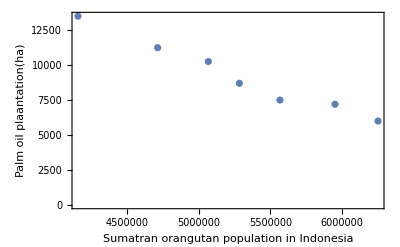

```mathematica
Block[{plantation,population},
plantation={4158077,4713431,5067058,5283557,5566635,5950349,6250460};
population={13500,11245,10254,8700,7500,7200,6000};
ListPlot[Thread@{plantation,population},Frame->True,FrameLabel->{"Sumatran orangutan population in Indonesia","Palm oil plaantation(ha)"}]
]
```

b.

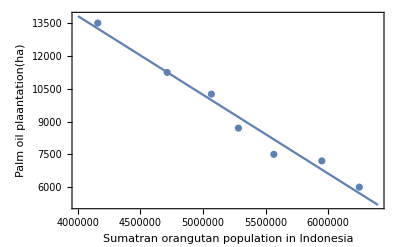

```mathematica
Block[{plantation,population,aa,bb,q,r,b,a},
plantation={4158077,4713431,5067058,5283557,5566635,5950349,6250460};
population={13500,11245,10254,8700,7500,7200,6000};
aa=Thread@{Table[1,Length@plantation],plantation};
bb=Transpose@{population};
{q,r}=QRDecomposition[aa];
{b,a}=Inverse[r].q.bb;
Show[
Plot[a x+b,{x,4 10^6,6.4 10^6}],
ListPlot[Thread@{plantation,population}],
PlotRange->All,Frame->True,FrameLabel->{"Sumatran orangutan population in Indonesia","Palm oil plaantation(ha)"}]
]
```

### Least Squares Regression Take 2

Exercises:

a, b.

```mathematica
Block[{plantation,population,aa,bb,a,b},
plantation={4158077,4713431,5067058,5283557,5566635,5950349,6250460};
population={13500,11245,10254,8700,7500,7200,6000};
aa=Thread@{Table[1,Length@plantation],plantation};
bb=Transpose@{population};
{b,a}=Inverse[Transpose[aa].aa].Transpose[aa].bb;
Show[
Plot[a x+b,{x,4 10^6,6.4 10^6}],
ListPlot[Thread@{plantation,population}],
PlotRange->All,Frame->True,FrameLabel->{"Sumatran orangutan population in Indonesia","Palm oil plaantation(ha)"}]
]
```

-Graphics-

c.

### Theorems and Problems

Problem 67. If A is an orthogonal square matrix then A^T=A^-1.

Problem 68. If A is an orthogonal square matrix then |A|=1.

## Lab 19: Symmetric Matrices and Quadratic Forms

### Introduction

Exercises:

a.

All eigenvectors are linearly independent. Therefore, A is diagonalizable.

```mathematica
SCARA[Eigenvectors[A],A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})]
SCMAF[%,RowReduce,All,Level->{1}]
```

Eigenvectors[A]=={{-1,-1,1},{1,1,2},{-1,1,0}}

RowReduce[Eigenvectors[A]]=={{1,0,0},{0,1,0},{0,0,1}}

```mathematica
D==Inverse[P].A.P
SCMAF[%,RA,{At[2],{A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}}),P==Transpose[{{-1,-1,1},{1,1,2},{-1,1,0}}]}},MatrixForm->True]
```

D==P^-1.A.P

D==(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

b.

```mathematica
Dot@@@Subsets[{{-1,-1,1},{1,1,2},{-1,1,0}},{2}]
```

{0,0,0}

c.

```mathematica
Normalize/@{{-1,-1,1},{1,1,2},{-1,1,0}}
```

{{-1/(√3),-1/(√3),1/(√3)},{1/(√6),1/(√6),√(2/3)},{-1/(√2),1/(√2),0}}

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}}),P==Transpose[{{-1/(√3),-1/(√3),1/(√3)},{1/(√6),1/(√6),√(2/3)},{-1/(√2),1/(√2),0}}]}},Apply->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

### Quadratic Forms

Exercises:

a.

Q_A is not bilinear.

```mathematica
Subscript[Q, A][u+v,w]==Subscript[Q, A][u,w]+Subscript[Q, A][v,w]
SCMAF[%,RA,{All,Subscript[Q, A][x1_,x2_]->x1^2+2x1 x2+x2^2},Apply->FullSimplify]
```

Q_A[u+v,w]==Q_A[u,w]+Q_A[v,w]

2 u v==w^2

```mathematica
Subscript[Q, A][k v,w]==k Subscript[Q, A][u,w]
SCMAF[%,RA,{All,Subscript[Q, A][x1_,x2_]->x1^2+2x1 x2+x2^2},Apply->FullSimplify]
```

Q_A[k v,w]==k Q_A[u,w]

(k v+w)^2==k (u+w)^2

b.

```mathematica
Subscript[Q, A][Subscript[x, 1],Subscript[x, 2]]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),A==({{1, 1}, {1, 1}})}},Apply->ExpandAll]
```

Q_A[x_1,x_2]==x^T.A.x

Q_A[x_1,x_2]=={{x_1^2+2 x_1 x_2+x_2^2}}

### Change of Variables in Quadratic Forms

Exercises:

a.

```mathematica
Subscript[Q, A][x]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}}),A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})}},Apply->ExpandAll]
```

Q_A[x]==x^T.A.x

Q_A[x]=={{3 x_1^2+4 x_1 x_2+3 x_2^2-2 x_1 x_3-2 x_2 x_3+4 x_3^2}}

b.

```mathematica
SCARA[Eigenvectors[A],A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})]
```

Eigenvectors[A]=={{-1,-1,1},{1,1,2},{-1,1,0}}

```mathematica
Normalize/@{{-1,-1,1},{1,1,2},{-1,1,0}}//MatrixForm
```

(-1/(√3) | -1/(√3) | 1/(√3)
1/(√6) | 1/(√6) | √(2/3)
-1/(√2) | 1/(√2) | 0)

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{P==Transpose[({{-1/(√3), -1/(√3), 1/(√3)}, {1/(√6), 1/(√6), √(2/3)}, {-1/(√2), 1/(√2), 0}})],A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})}},Apply->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

```mathematica
Subscript[Q, A][y]==Transpose[y].Transpose[P].A.P.y
SCMAF[%,RA,{At[2],Transpose[P].A.P==D},
RA,{At[2],{y==({{Subscript[y, 1]}, {Subscript[y, 2]}, {Subscript[y, 3]}}),D==({{6, 0, 0}, {0, 3, 0}, {0, 0, 1}})}},Apply->ExpandAll]
```

Q_A[y]==y^T.P^T.A.P.y

Q_A[y]==y^T.D.y

Q_A[y]=={{6 y_1^2+3 y_2^2+y_3^2}}

c.

```mathematica
SCARA[Eigenvectors[A],A==({{1, 1}, {1, 1}})]
```

Eigenvectors[A]=={{1,1},{-1,1}}

```mathematica
Normalize/@{{1,1},{-1,1}}//MatrixForm
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{P==Transpose[({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}})],A==({{1, 1}, {1, 1}})}},Apply->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(2 | 0
0 | 0)

```mathematica
Subscript[Q, A][y]==Transpose[y].Transpose[P].A.P.y
SCMAF[%,RA,{At[2],Transpose[P].A.P==D},
RA,{At[2],{y==({{Subscript[y, 1]}, {Subscript[y, 2]}}),D==({{2, 0}, {0, 0}})}},Apply->ExpandAll]
```

Q_A[y]==y^T.P^T.A.P.y

Q_A[y]==y^T.D.y

Q_A[y]=={{2 y_1^2}}

d.

### Principal Axes Theorem

Example:

```mathematica
SCARA[Eigensystem[A],A==({{3, -2}, {-2, 3}})]
```

Eigensystem[A]=={{5,1},{{-1,1},{1,1}}}

```mathematica
Normalize/@{{-1,1},{1,1}}//MatrixForm
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{P==Transpose@({{-1/(√2), 1/(√2)}, {1/(√2), 1/(√2)}}),A==({{3, -2}, {-2, 3}})}},Apply->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(5 | 0
0 | 1)

```mathematica
Subscript[Q, A][y]==Transpose[y].D.y
SCMAF[%,RA,{At[2],{y==({{Subscript[y, 1]}, {Subscript[y, 2]}}),D==({{5, 0}, {0, 1}})}}]
```

Q_A[y]==y^T.D.y

Q_A[y]=={{5 y_1^2+y_2^2}}

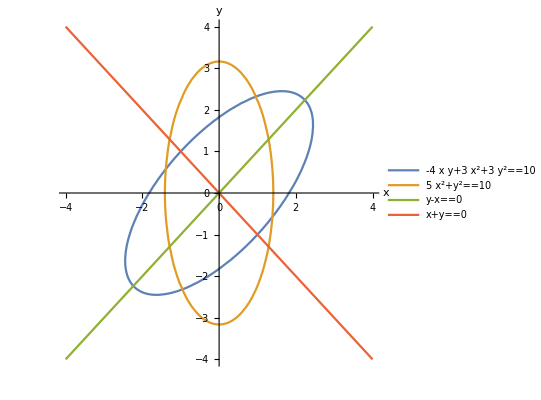

```mathematica
ContourPlot[{3 x^2-4x y+3 y^2==10,5 x^2+y^2==10,y-x==0,y+x==0},{x,-4,4},{y,-4,4},Axes->True,Frame->False,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

### Properties of Quadratic Forms

Exercises:

a.

```mathematica
Subscript[Q, A][x]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),A==({{1, 0}, {0, 1}})}}]
```

Q_A[x]==x^T.A.x

Q_A[x]=={{x_1^2+x_2^2}}

b.

```mathematica
Subscript[Q, A][x]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),A==({{-1, 0}, {0, -1}})}}]
```

Q_A[x]==x^T.A.x

Q_A[x]=={{-x_1^2-x_2^2}}

c.

```mathematica
SCARA[Eigenvalues[A],A==({{1, 2}, {2, 1}})]
```

Eigenvalues[A]=={3,-1}

```mathematica
SCARA[Eigenvalues[A],A==({{-1, 0}, {0, -1}})]
```

Eigenvalues[A]=={-1,-1}

Exercises:

a.

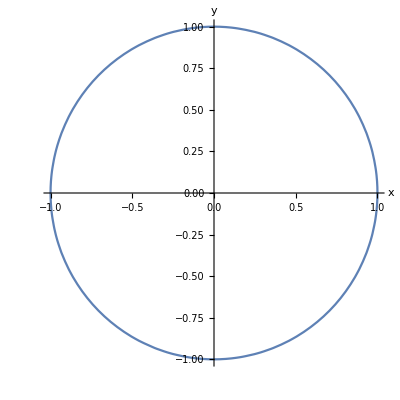

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},Frame->False,Axes->True,AxesLabel->Automatic]
```

b.

Demonstration: Conic Sections: Equations and Graphs

c.

d.

e.

### Theorems and Problems

Theorem 69. If A is symmetric then any two eigenvectors of A are orthogonal.

Theorem 70. If A is symmetric then A is orthogonally diagonalizable.

Problem 71. If Q(x_1,x_2,x_3, …, x_n) is a quadratic form with all real coefficients then it is positive definite iff
Q(x_1,x_2,x_3,…,x_n)=x_1^2+x_2^2+x_3^2+…+x_n^2.

Theorem 72. A quadratic form Q is positive definite iff the eigenvalues of the coefficient matrix A are all positive.

Theorem 73. If A is a positive or negative definite matrix then A is invertible.

Problem 74. If A is a symmetric 2×2 matrix with eigenvalues λ_1≥λ_2 and Q_A is the quadratic form defined by Q_A(x)=x^T A x, then the conic section defined by Q_A(x)=1 is
(1) an ellipse if λ_1≥λ_2>0.
(2) a hyperbola if λ_1>0>λ_2,
(3) the empty set if 0≥λ_1≥_2 and
(4) two parallel lines if λ_1>λ_2=0.